```mathematica
f[r_,Q_] = 1-2/r+Q^2/r^2;
```

```mathematica
rr[Q_]=r/.Solve[f[r,Q]==0,r]
```

{1-√(1-Q^2),1+√(1-Q^2)}

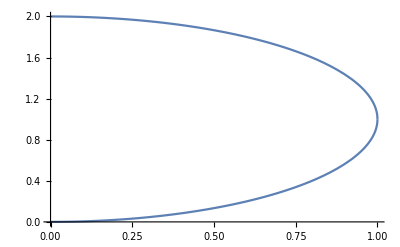

```mathematica
Plot[rr[Q],{Q,0,1}]
```

```mathematica
f[r_,α_] := 1 - (2(1+α))/r+(α(1+α))/r^2
```

```mathematica
U[r_,α_,ω_,L_] := α/r - Sqrt[f[r,α] (1+((L - ω(r^2-α(1+α)))^2)/r^2)]
```

```mathematica
u[r_,α_,L_] := α/r + Sqrt[f[r,α] (1+L^2/r^2)]
```

```mathematica
U1[r_,α_,ω_,L_] := α/r + Sqrt[f[r,α] (1+((L - ω(r^2-α(1+α)))^2)/r^2)]
```

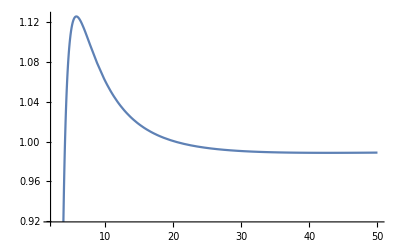

```mathematica
Plot[u[r,1,7],{r,2,50}]
```

```mathematica
Clear[l]
```

```mathematica
l[α_,ω_]:=L/.Solve[D[U[r,α,ω,L],r]==0,L][[1]]
```

```mathematica
rr[α_,ω_]:=r/.FindRoot[D[l[α,ω],r]==0,{r,6}]
```

```mathematica
Table[rr[i,0],{i,0,1,0.005}]
rr[0.1,0.1]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{6.,6.02249,6.04498,6.06745,6.08991,6.11236,6.13479,6.15722,6.17963,6.20204,6.22443,6.24681,6.26918,6.29154,6.31389,6.33623,6.35856,6.38088,6.40319,6.42549,6.44778,6.47006,6.49233,6.51459,6.53684,6.55908,6.58132,6.60354,6.62575,6.64796,6.67015,6.69234,6.71451,6.73668,6.75884,6.78099,6.80313,6.82526,6.84739,6.8695,6.89161,6.91371,6.9358,6.95788,6.97996,7.00202,7.02408,7.04613,7.06817,7.09021,7.11223,7.13425,7.15626,7.17826,7.20026,7.22225,7.24423,7.2662,7.28817,7.31013,7.33208,7.35402,7.37596,7.39789,7.41981,7.44173,7.46364,7.48554,7.50744,7.52933,7.55121,7.57308,7.59495,7.61681,7.63867,7.66052,7.68236,7.7042,7.72603,7.74785,7.76967,7.79148,7.81328,7.83508,7.85687,7.87866,7.90044,7.92222,7.94398,7.96575,7.9875,8.00926,8.031,8.05274,8.07447,8.0962,8.11792,8.13964,8.16135,8.18306,8.20476,8.22645,8.24814,8.26983,8.29151,8.31318,8.33485,8.35651,8.37817,8.39982,8.42147,8.44311,8.46475,8.48638,8.50801,8.52963,8.55125,8.57286,8.59447,8.61607,8.63767,8.65926,8.68085,8.70243,8.72401,8.74558,8.76715,8.78872,8.81028,8.83183,8.85339,8.87493,8.89647,8.91801,8.93955,8.96107,8.9826,9.00412,9.02563,9.04715,9.06865,9.09016,9.11165,9.13315,9.15464,9.17613,9.19761,9.21909,9.24056,9.26203,9.2835,9.30496,9.32641,9.34787,9.36932,9.39076,9.41221,9.43364,9.45508,9.47651,9.49794,9.51936,9.54078,9.56219,9.5836,9.60501,9.62642,9.64782,9.66921,9.69061,9.712,9.73338,9.75477,9.77614,9.79752,9.81889,9.84026,9.86162,9.88299,9.90434,9.9257,9.94705,9.9684,9.98974,10.0111,10.0324,10.0538,10.0751,10.0964,10.1177,10.1391,10.1604,10.1817,10.203,10.2243,10.2456,10.2669,10.2882,10.3095,10.3308,10.3521}

$Aborted

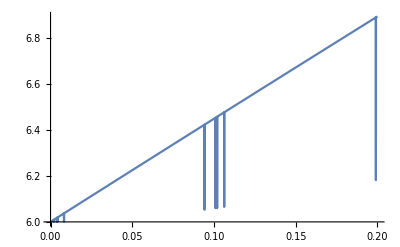

```mathematica
Plot[rr[α,0],{α,0,0.2}]
```